## Smn1 visualization

```mathematica
cartoon12=ImageCrop@Import["5ss_cartoon_canonical_-1+5.png"];
cartoon13=ImageCrop@Import["5ss_cartoon_canonical_+3.png"];
```

### Visualization Functions

```mathematica
Nbysum[y_]:=(1/Total[y])*y
```

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
FixationProb[oldfitness_,newfitness_,c_]:=Module[{S},
S=c*(newfitness-oldfitness);
If[S==0,1,S/(1-E^-S)]
]
```

```mathematica
QMatrixMutSparse[c_,fitnessvec_,adj_]:=Module[{output,rules},
rules=Most[ArrayRules[adj]];
output=SparseArray[
Table[rules[[i,1]]-> FixationProb[fitnessvec[[rules[[i,1,1]] ]],fitnessvec[[rules[[i,1,2]] ]],c],
{i,Length[rules]}]
,{Length[adj],Length[adj]}];
output=1/(alpha-1)(-MakeDiagonal[Total/@output]+output)
]
```

```mathematica
MakeNormalized[vect_,mat_]:=MakeDiagonal[vect^(1/2)].(mat.MakeDiagonal[vect^-(1/2)])
```

```mathematica
EigenDecompPart[stationary_,P_,num_]:=Module[{normalized,vals,vecs,invals},
normalized=MakeNormalized[stationary,P];
{vals,vecs}=Eigensystem[normalized,num,Method->{Automatic,Tolerance->10^-15,MaxIterations->100000}];
Do[vecs[[i]]=Normalize[vecs[[i]]],{i,1,Length[vecs]}];
(*Changed function so that the vectors are explicitly normalized -- exact evaluation leads to eigenvectors that are simple but not of length 1. August 2, 2009*)
invals=1/(-vals[[2;;]]);
invals=Prepend[invals,0];
{vals,invals,MatrixForm[Transpose[vecs]],MatrixForm[MakeDiagonal[stationary^(-1/2)]. Transpose[vecs]]}
(*NB Vectors are in columns!*)
]
```

### Embedding coordinates

```mathematica
map =Import["output_python/map_all_data.tsv","TSV"]//Flatten;
```

```mathematica
truncate[fit_]:=If[fit<0,0,If[fit>100,100,fit]]
```

```mathematica
fitness=truncate/@map; (*Fitness function used for visualization*)
```

```mathematica
fitness[[Join[seqlistNGU,seqlistAG]]] = 0; (*set sequences with secondary GU and +2A/G to zero*)
```

```mathematica
c=.066;
Stat=Nbysum@Table[E^(c*fitness[[i]]),{i,Length[fitness]}];
Stat.fitness
```

79.2183

```mathematica
Qmat=QMatrixMutSparse[c,fitness,Adj];//AbsoluteTiming (*Q:rate matrix of the continuous time Markov chain*)
```

{14.89,Null}

```mathematica
r=Table[Abs@Qmat[[i,i]],{i,Length[Qmat]}]//Max
```

21.5125

```mathematica
Stat=Nbysum@Table[E^(c*fitness[[i]]),{i,Length[fitness]}];
```

```mathematica
Eig=EigenDecompPart[Stat,MakeDiagonal[Table[2r,alpha^l]]+Qmat,10];//AbsoluteTiming
Eigvecs=Replace[Eig[[4]],MatrixForm[a_,___]:>a];
```

{18.9865,Null}

```mathematica
Eigenvals=Rest[Eig[[1]]]-2r
```

{-0.191639,-0.379631,-0.528973,-0.598217,-0.623319,-0.728558,-0.844411,-0.898572,-0.899931}

```mathematica
Eigvecs2=Eigvecs.MakeDiagonal[Prepend[1/(Sqrt[-Eigenvals]),0]];
```

```mathematica
coorsubs=Eigvecs2[[All,2;;4]];
```

```mathematica
Table[(Qmat.Eigvecs[[All,i]])[[1]]/Eigvecs[[All,i]][[1]],{i,2,10}]
```

{-0.191639,-0.379631,-0.528973,-0.598217,-0.623319,-0.728558,-0.844411,-0.898572,-0.899931}

```mathematica
Eigenvals
```

{-0.191639,-0.379631,-0.528973,-0.598217,-0.623319,-0.728558,-0.844411,-0.898572,-0.899931}

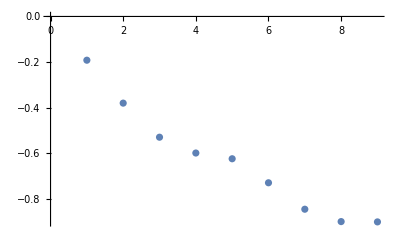

```mathematica
ListPlot[Eigenvals ]
```

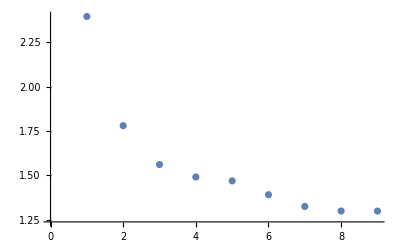

```mathematica
ListPlot[1/Sqrt@(1-E^Eigenvals) ]
```

### hg38 counts for coloring 5’ss

```mathematica
sub=Complement[Range[alpha^l],seqlistAG];
```

```mathematica
seqAA2num[seq_]:=Characters[seq][[{1,2,3,6,7,8,9,10}]]/.{"T"->"U"}/.AAtoDigitRules
```

```mathematica
counts=Import["data/human_5ss.txt","TSV"];
counts[[2;;,-1]];
Table[seqAA2num[seq],{seq,%}];
seq2pos/@%;
Tally[%];
{pos, counts} = {%[[All,1]],%[[All,2]]};
```

```mathematica
1 - Length[counts]/32768//N
```

0.659241

```mathematica
countsfull = MapPartialVal[pos, counts,alpha^l];
```

```mathematica
colorfunc[x_]:=Blend[{Black,Blue},x]
```

```mathematica
(*colorfunc[x_]:=ColorData["TemperatureMap"][x]*)
```

```mathematica
colors=N@Rescale[Log@counts];
colorsfull=MapPartialVal[pos, colors,alpha^l];
colordata=If[# ==0., GrayLevel[RandomReal[{.35,.55}]], colorfunc[#]]&/@colorsfull;
```

```mathematica
{min,max}={Log10[counts]//Min, Log10[counts]//Max};
```

```mathematica
logTicks[min_,max_]:={#,10^#}&/@FindDivisions[{min,max},5]
```

```mathematica
legend=BarLegend[{colorfunc[#/(max-min)]&,{min,max}},LabelStyle->Directive[GrayLevel[.25],FontSize->labfontsize],LegendMarkerSize->{200,10},LegendLayout->"Row",Ticks->logTicks[min,max],LegendMargins->0,LegendLabel->Placed[TextGrid[{Style[#,FontSize->labfontsize,FontFamily->"Helvetica"]&/@{ "counts  "}},Spacings->.2],Bottom]]
```

```mathematica
f = max - min//N;
binwidth=.2;
```

```mathematica
hist = Module[{dist},dist=BinCounts[f *colors,{min,max,binwidth}];
dist=dist/Total[dist];
Graphics[Table[{colorfunc[(Range[min,max,binwidth][[i]] +binwidth/2)/f],Rectangle[{i+.5,dist[[i]]},{i-.5,0}]},{i,(max-min)/binwidth}],AspectRatio->.2
, ImageSize->184,ImageMargins->{{14,0},{0,0}}]
];
```

```mathematica
zerolegend=BarLegend[{Gray&,{-.5,.5}},LabelStyle->Directive[GrayLevel[.25],FontSize->labfontsize],LegendMarkerSize->{30,35},LegendLayout->"Row",Ticks->{{0,0}},LegendLabel->Placed[TextGrid[{Style[#,FontSize->14,Transparent,FontFamily->"Helvetica"]&/@{ "c "}},Spacings->.2],Bottom]];
```

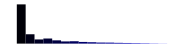
| -Graphics-
 |

```mathematica
barhist = Grid[{{Null,hist},{zerolegend,legend}},Spacings->{-1.1,-.8}]
```

### Plotting parameters

```mathematica
ordering=SortBy[Transpose@{Complement[Range[alpha^l],seqlistAG],countsfull[[Complement[Range[alpha^l],seqlistAG]]]},Last][[All,1]];
```

```mathematica
fontsize=27;
tickstyle=Directive[fontsize];
fstyle=Table[{GrayLevel[.3],AbsoluteThickness[1],FontSize->fontsize},4];
```

#### Plot ranges

```mathematica
padding=0.5;
pr12={{Min@coorsubs[[All,1]] - padding,Max@coorsubs[[All,1]] + padding},{Min@coorsubs[[All,2]] - padding,Max@coorsubs[[All,2]] + padding}};
pr13={{Min@coorsubs[[All,1]] - padding,Max@coorsubs[[All,1]] + padding},{Min@coorsubs[[All,3]] - padding,Max@coorsubs[[All,3]] + padding}};
pr23={{Min@coorsubs[[All,2]] - padding,Max@coorsubs[[All,2]] + padding},{Min@coorsubs[[All,3]] - padding,Max@coorsubs[[All,3]] + padding}};
```

#### Plotting parameters

```mathematica
para12={Frame->True,
FrameStyle->fstyle,
FrameTicksStyle->tickstyle,
PlotRange->pr12,
FrameTicks->{{Range[-10,10,2],None},{Range[-10,10,2],None}},
PlotRangePadding->None,
ImageSize->700,
FrameLabel->{Style["Diffusion axis 1", fontsize],Style["Diffusion axis 2", fontsize]}
};
para13={Frame->True,
FrameStyle->fstyle,
FrameTicksStyle->tickstyle,
PlotRange->pr13,
FrameTicks->{{Range[-10,10,2],None},{Range[-10,10,2],None}},
PlotRangePadding->None,
ImageSize->700,
FrameLabel->{Style["Diffusion axis 1", fontsize],Style["Diffusion axis 3", fontsize]}
};
```

```mathematica
para12noframe={Frame->None,
PlotStyle->PointSize[.1],
PlotRange->pr12,
PlotRangePadding->None,
ImageSize->700
};
```

```mathematica
para13noframe={Frame->None,
PlotRange->pr13,
PlotRangePadding->None,
ImageSize->700
};
```

```mathematica
sf=700;
```

```mathematica
size12=sf{1,(pr12[[2]][[2]]-pr12[[2]][[1]])/(pr12[[1]][[2]]-pr12[[1]][[1]])};
size13=sf{1,(pr13[[2]][[2]]-pr13[[2]][[1]])/(pr13[[1]][[2]]-pr13[[1]][[1]])};
size23=size13[[2]]{(pr23[[1]][[2]]-pr23[[1]][[1]])/(pr23[[2]][[2]]-pr23[[2]][[1]]),1};
```

#### Font sizes

```mathematica
labfontsize=18;
lgmsize=16;
```

#### Dot colors

```mathematica
(*orange=1.2*{255,131,0}/255;
red=1.2{215,48,31}/255;
yellow=1.1{249/255,216/255,73/255};
gray={.8,.8,.8};*)
```

```mathematica
(*orange={240,130,0}/255;
red={215,10,10}/255;
yellow={230/255,216/255,0/255};

(*green=0.8{103/255,202/255,77/255};*)*)
```

```mathematica
red=0.8{2/3,0,0};
orange=0.8{253,141,0}/255;
yellow=0.9{230/255,216/255,0/255};
gray={.8,.8,.8};
```

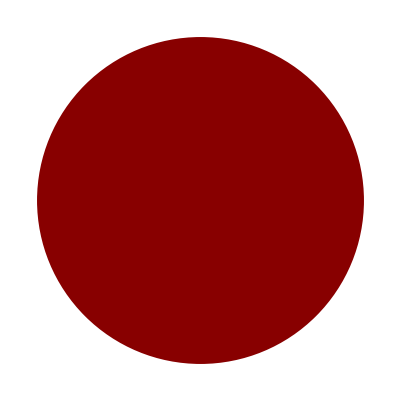

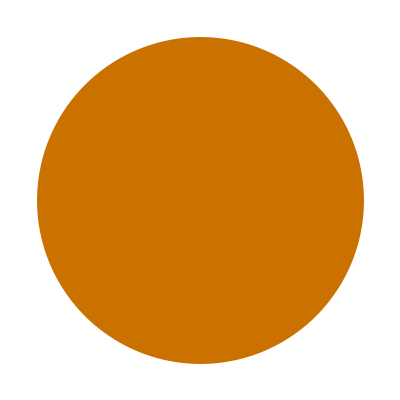

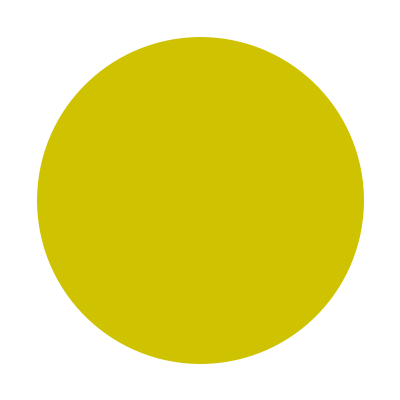

```mathematica
Graphics[{Darker[RGBColor@red,0],Disk[]}]
Graphics[{Darker[RGBColor@orange,0],Disk[]}]
Graphics[{Darker[RGBColor@yellow,0],Disk[]}]
```

#### color data for DA2 vs. DA1

```mathematica
motifQ[seq_]:={seq[[positions[[1]]]]==motif[[1]],seq[[positions[[2]]]]==motif[[2]]}
```

```mathematica
colorrules={{True,True}->orange,{True,False}->red,{False,True}->yellow,{False,False}->gray};
positions={3,-2};
motif={2,2};
colordata12=(motifQ/@sequences)/.colorrules;
colordata12=colordata12+RandomReal[.5{-.1,.1},Length[colordata12]];
colordata12=RGBColor/@colordata12;
```

#### Color data for DA3 vs. DA1

```mathematica
color13={red,yellow};
colordata13=#==0/.{True-> color13[[1]],False->color13[[2]]}&/@sequences[[All,5]];
colordata13=colordata13+RandomReal[{-.1,.1},Length[colordata13]];
colordata13=RGBColor/@colordata13;
```

#### Color legends

```mathematica
textlabels=Style[#,FontFamily->"Helvetica",FontSize->labfontsize-1,Black]&/@{"(G, G)","(G, Not G)","(Not G, G)","(Not G, Not G)"};
key12=Column[{Style["Alleles at (-1, +5)",FontFamily->"Helvetica",FontSize->labfontsize,Black],PointLegend[RGBColor/@colorrules[[All,2]],textlabels,Spacings->0,LegendMargins->0,LegendMarkerSize->lgmsize]},Left,Spacings->0.1]
```

Alleles at (-1, +5)

```mathematica
textlabelsbase=Style[#,FontFamily->"Helvetica",FontSize->labfontsize-1,Black]&/@{"A","Not A"};
key13=Column[{Style["Alleles at +3",FontFamily->"Helvetica",FontSize->labfontsize,Black],PointLegend[RGBColor/@color13,textlabelsbase,Spacings->0,LegendMargins->0,LegendMarkerSize->lgmsize]},Left,Spacings->0.1]
```

Alleles at +3

#### Extract edges from Adjacency matrix for later plotting

```mathematica
edges=Most[ArrayRules[Adj][[All,1]]];
edges=DeleteDuplicates[Sort/@edges];
edges=Select[edges,SubsetQ[{1,3},sequences[[#]][[All,4]]]&];
Length@edges
```

360448

#### Pick subset of sequences with PSI>80

```mathematica
fitcolor=fitness;
Do[fitcolor[[i]]=responseSmn1[[i]],{i,seqlistSmn1}];
fitcolor=truncate/@fitcolor;
Do[fitcolor[[i]]=0,{i,seqlistNGU}]
Do[fitcolor[[i]]=0,{i,seqlistAG}]
```

```mathematica
seqlistsub=Select[seqlistAll,fitcolor[[#]]>80&];
```

#### Use uniform imagepadding to align

```mathematica
imagepadding={{95,10},{80,10}};
```

### Make rasterized background with edges

#### DA2 vs DA1

```mathematica
i=1
```

1

```mathematica
bg12=Rasterize[Show[
(*Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Transparent,Rectangle[points[[1]],points[[-1]]]}]*)
Graphics[Table[{GrayLevel[.5,.3],Thickness[.0005],Line[coorsubs[[edges[[i]],{1,2}]]]},{i,Length@edges}]],
para12noframe
],RasterSize->2000];
```

#### DA3 vs DA1

```mathematica
bg13=Rasterize[Show[
(*Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Transparent,Rectangle[points[[1]],points[[-1]]]}]*)
Graphics[Table[{GrayLevel[.5,.3],Thickness[.0005],Line[coorsubs[[edges[[i]],{1,3}]]]},{i,Length@edges}]],
para13noframe
],RasterSize->2000];
```

### Panel A: DA1 v. DA2

#### Plotting inset

```mathematica
fig12inset=Show[Graphics[Table[{colordata12[[i]],PointSize[.008],Point[coorsubs[[i,{1,2}]]]},{i,ordering}]],
para12noframe,
Prolog->Inset[bg12,Scaled[{0,0}],ImageScaled[{0,0}],Scaled[1]]
];
```

```mathematica
fig12insetr=Rasterize[fig12inset,RasterSize->2000];
```

#### Plotting main panel

```mathematica
fig12=Show[Graphics[Table[{colordata[[i]],PointSize[.0065],Point[coorsubs[[i,{1,2}]]]},{i,Length@coorsubs}]],
para12,
ImagePadding->imagepadding,
Prolog->{Inset[bg12,Scaled[{0,0}],ImageScaled[{0,0}],Scaled[1]],
Inset[fig12insetr,{-8.3,2.3},{0,0},3.5],
Inset[barhist,{-6.5,-1.6}],
Inset[cartoon12,{-3.7,4.4},Center,2.4],
Inset[key12,{-3.7,2.8}]}
];
```

### Panel B: DA3 v. DA1

#### Plotting inset

```mathematica
fig13inset=Show[Graphics[Table[{colordata13[[i]],PointSize[.0065],Point[coorsubs[[i,{1,3}]]]},{i,ordering}]],
para13noframe,
Prolog->Inset[bg13,Scaled[{0,0}],ImageScaled[{0,0}],Scaled[1]]
];
```

```mathematica
fig13insetr=Rasterize[fig13inset,RasterSize->2000];
```

#### Plotting main panel

```mathematica
fig13=Show[Graphics[Table[{colordata[[i]],PointSize[.0065],Point[coorsubs[[i,{1,3}]]]},{i,ordering}]],
para13,
ImagePadding->imagepadding,
Prolog->{
Inset[bg13,Scaled[{0,0}],ImageScaled[{0,0}],Scaled[1]],
Inset[fig13insetr,{-8.2,1.7},{0,0},3.5],
Inset[cartoon13,{-3.7,3.5},Center,2.2],
Inset[key13,{-4.0,2.3}]
(*,
Text[Style["B",Bold,FontFamily->"Helvetica", FontSize->fontsize],ImageScaled@{.04,.95}]*)}
];
```

### Panel C: PSI v. DA1

```mathematica
parapsi={PlotRange->{pr13[[1]],{0,105}},
PlotRangePadding->None,
ImagePadding->imagepadding,
Axes->False,
Frame->True,
FrameStyle->fstyle,
FrameTicks->{{Range[0,100,20],None},{Range[-10,10,2],None}},
FrameTicksStyle->tickstyle,
ImageSize->700,
FrameLabel->{Style["Diffusion axis 1", fontsize],Style["PSI", fontsize]},
FrameTicksStyle->tickstyle,
AspectRatio->size13[[2]]/size13[[1]]};
```

```mathematica
fig1psi=Show[
Graphics[Table[{colordata[[i]],PointSize[.0065],Point[{coorsubs[[i,1]],fitness[[i]]}]},{i,ordering}]],
parapsi
];
```

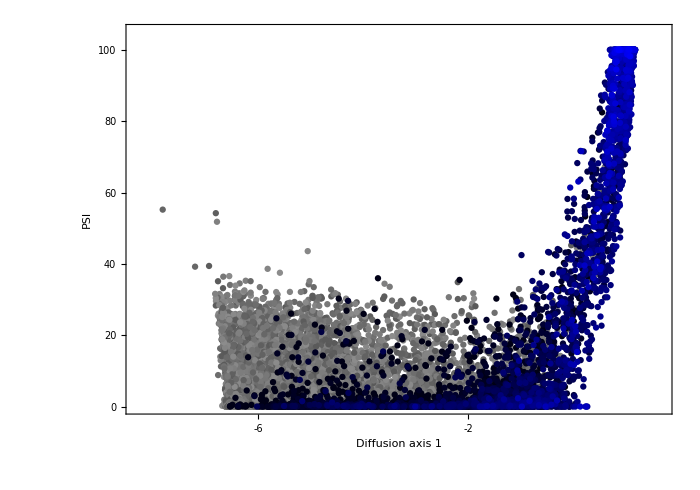

```mathematica
fig1psi
```

### Panel D: DA2 vs. Physical position

```mathematica
wtnum=Characters[wt]/.AAtoDigitRules
```

{1,0,2,3,0,0,2,3}

Function to extract mismatch / match positions

```mathematica
mispos[seq_]:=Flatten@Position[Table[seq[[i]]==wtnum[[i]],{i,Range[l]}],False]/.Table[i->If[i>3,i+1,i],{i,l}]
conpos[seq_]:=Flatten@Position[Table[seq[[i]]==wtnum[[i]],{i,Range[l]}],True]/.Table[i->If[i>3,i+1,i],{i,l}]
```

#### Mean match pos

```mathematica
plotdat=Transpose@{Mean/@conpos/@sequences[[seqlistsub]],coorsubs[[seqlistsub,2]]};
```

#### Maximize alignment between axes

```mathematica
height=.5 ImageDimensions[fig12][[2]] (*use height of panel A*)
```

567.

```mathematica
pry=pr12[[2]] (*y plot range = y plot range in panel 1*)
```

{-2.88275,5.14198}

```mathematica
(*datda2rescaled=(plotdat[[All,2]]-pr12[[2]][[1]])/(First@Differences@pr12[[2]]);*)
```

```mathematica
(*NMinimize[Total@Table[(((plotdat[[i,1]]-b))/(a-b)   - datda2rescaled[[i]])^2,{i,Length[plotdat]}],{a,b}]*)
```

```mathematica
(*%[[2,All,2]]*)
```

```mathematica
(*prx=Reverse@%*)
```

```mathematica
xpositions={"-3","-2","-1","+1","+2","+3","+4","+5","+6"};
```

```mathematica
prx={Min[#],Max[#]}&@plotdat[[All,1]]//N;
prx=prx+{-.2,+.2};
```

Use height of panel 1

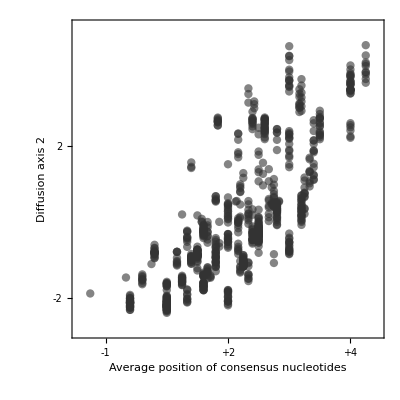

```mathematica
figpp=Show[ListPlot[
plotdat,
PlotStyle->{GrayLevel[.2,.6],PointSize[.015]},
Frame->True,
FrameStyle->fstyle,
FrameTicksStyle->tickstyle,
PlotRange->{prx,pry},
PlotRangeClipping->None,
FrameTicks->{{Range[-10,10,2],None},{Table[{i,xpositions[[i]]},{i,Length[xpositions]}],None}},
PlotRangePadding-> None,
ImagePadding->imagepadding,
ImageSize->{Automatic,height},
AspectRatio->1,
Axes->False,
FrameLabel->{Style["Average position of consensus nucleotides", fontsize],
Style["Diffusion axis 2", fontsize]}
]]
```

### Panel E: DA3 vs. DA2

```mathematica
(*ImageDimensions[fig13]*)
```

```mathematica
(*ImageDimensions[fig2pp]*)
```

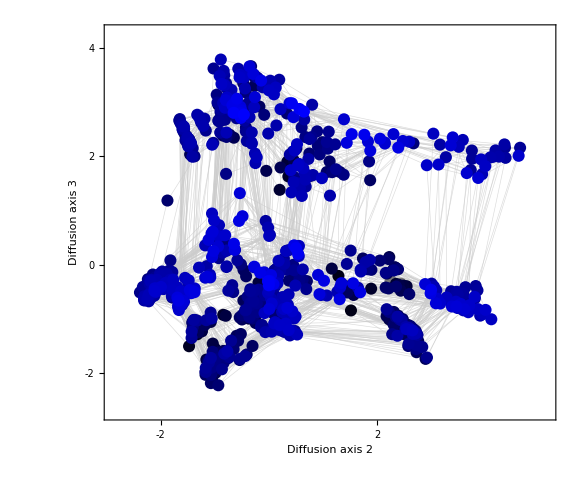

```mathematica
sub=seqlistsub;
sub=SortBy[Transpose@{sub,countsfull[[sub]]},Last][[All,1]];
fig23=Show[
GraphPlot[
Adj[[sub,sub]],
VertexCoordinates->coorsubs[[sub,{2,3}]],
VertexShapeFunction->Function[{p,l},{Point[p]}],
PlotStyle->{GrayLevel[.8],Thickness-> .8 10^-3},
Frame->True,
FrameTicksStyle->tickstyle,
FrameStyle->fstyle,
PlotRange->pr23,
FrameTicks->{{Range[-10,10,2],None},{Range[-10,10,2],None}},
PlotRangePadding->None,
ImagePadding->imagepadding,
ImageSize->{1158/2,994/2}(*width: panel D, height: panel B*),
FrameLabel->{Style["Diffusion axis 2", fontsize],Style["Diffusion axis 3", fontsize]}
],
Table[Graphics[{colordata[[i]],PointSize[.015],Point[coorsubs[[i,{2,3}]]]}],{i,sub}]]
```

### Panel F: DA3 v. DA2 - Matchstick figure

```mathematica
associate[tab1_,tab2_]:=Table[tab1[[i]]->tab2[[i]],{i,Length[tab1]}]
```

```mathematica
labels=Table[StringRiffle[Table[If[site<0,ToString[site],"+"<>ToString[site]],{site,MutatedSites}],""],{MutatedSites,{{},{-1},{5},{3},{-1,3},{3,5}}}]; (*make labels for each mutant group*)
```

```mathematica
sites={-3,-2,-1,+2,+3,+4,+5,+6};
subsites={-2,-1,+4,+5,+6};
```

```mathematica
mutsitelists3A=Subsets[subsites,{0,5}]; (*all subsets of sites with +3A*)
mutsitelists3mut=Sort[Join[{+3},#]]&/@Subsets[subsites,{0,5}] (*all subsets of sites with +3mut*);
```

```mathematica
seqwt=sequences[[seq2pos9AA["CAGGUAAGU"]]];
siterules=Table[{-3,-2,-1,+1,+2,+3,+4,+5,+6}[[i]]->i,{i,9}];
siterules2=Table[{-3,-2,-1,+2,+3,+4,+5,+6}[[i]]->i,{i,8}];
mutsub[sites_]:=seq2pos/@Tuples[ReplacePart[Subsets[seqwt,{1}],Join[Table[i->Complement[A,{seqwt[[i]]}],{i,(sites/.siterules2)}],{(-3/.siterules2)->A}]]] (*return list of mutant 5'ss given subset of sites*)
```

```mathematica
MutatedSitesList=Join[mutsitelists3A,mutsitelists3mut]; (*All mutant groups to be plotted*)
```

```mathematica
presenceabsence=Table[ReplacePart[ConstantArray[0,9],Table[(i/.siterules)->1,{i,MutatedSitesList[[j]]}]],{j,Length[MutatedSitesList]}];(*binary encoding mutant groups*)
mutlist=Table[Intersection[seqlistsub,mutsub[MutatedSitesList[[i]]]],{i,Length[MutatedSitesList]}]; (*list of 5'ss in each mutant group*)
coords=Table[Mean[coorsubs[[i,{2,3}]]],{i,mutlist}];(*centroids for each mutant group*)
sub=Select[Range[Length[MutatedSitesList]],Length[mutlist[[#]]]>0&]; (*keep mutant groups with at least one 5'ss with PSI>80*)
g=DeleteDuplicates[Sort/@Complement[Flatten@Table[If[HammingDistance[presenceabsence[[i]],presenceabsence[[j]]]==1,i<->j,i<->i],{i,sub},{j,sub}],Table[i<->i,{i,Length[MutatedSitesList]}]]]; (*make graph for subset of mutant groups*)
```

```mathematica
(*make dark edges within *)
s=Subsets[Flatten[Position[mutsitelists3A,#]&/@Sort/@(Join[{},#]&/@Subsets[{-2,+4,+6}])],{2}];
s5=Subsets[Flatten[Position[mutsitelists3A,#]&/@Sort/@(Join[{+5},#]&/@Subsets[{-2,+4,+6}])],{2}];
s1=Subsets[Flatten[Position[mutsitelists3A,#]&/@Sort/@(Join[{-1},#]&/@Subsets[{-2,+4,+6}])],{2}];
s15=Subsets[Flatten[Position[mutsitelists3A,#]&/@Sort/@(Join[{-1,+5},#]&/@Subsets[{-2,+4,+6}])],{2}];
smut=Subsets[Flatten[Position[Join[mutsitelists3A,mutsitelists3mut],#]&/@Sort/@(Join[{+3},#]&/@Subsets[{-2,+4,+6}])],{2}];
s5mut=Subsets[Flatten[Position[Join[mutsitelists3A,mutsitelists3mut],#]&/@Sort/@(Join[{+5,+3},#]&/@Subsets[{-2,+4,+6}])],{2}];
s1mut=Subsets[Flatten[Position[Join[mutsitelists3A,mutsitelists3mut],#]&/@Sort/@(Join[{-1,+3},#]&/@Subsets[{-2,+4,+6}])],{2}];
s15mut=Subsets[Flatten[Position[Join[mutsitelists3A,mutsitelists3mut],#]&/@Sort/@(Join[{-1,+3,+5},#]&/@Subsets[{-2,+4,+6}])],{2}];
```

```mathematica
edges=Join[s, s1, s5, smut,s1mut,s5mut];
```

```mathematica
edges=Table[edges[[i]][[1]]<->edges[[i]][[2]],{i,Length[edges]}];
```

```mathematica
labcoords=Table[Mean[coorsubs⟦seqlistsub∩mutsub[MutatedSites],{2,3}⟧],{MutatedSites,{{},{-1},{5},{3},{-1,3},{3,5}}}]+{{0,0},{.2,-.7},{-.5,-.8},{0,.4},{.3,.3},{-.9,.2}}; (*coordinates of mutant group labels*)
```

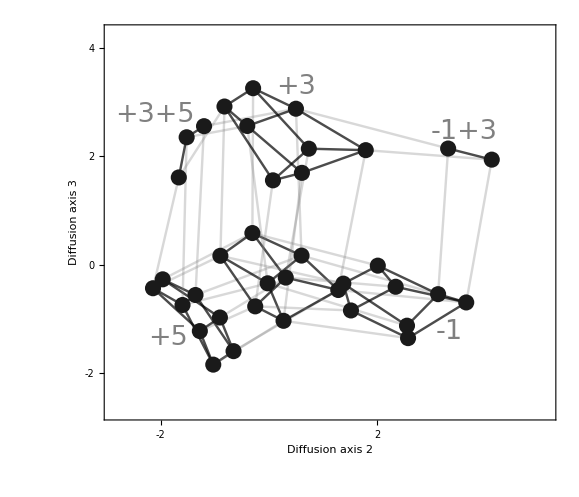

```mathematica
figstick=Show[
GraphPlot[g,
VertexCoordinates->associate[Range[Length[MutatedSitesList]][[sub]],coords[[sub]]],
VertexShapeFunction->Function[{p,l},{Tooltip[Point[p],MutatedSitesList[[l]],TooltipStyle->Directive[Black, Bold,20]]}],
EdgeShapeFunction->(If[edges∩{#2}≠{},{Black,Line[#1]},{GrayLevel[.5,.3],Line[#1]}]&),
PlotStyle->{GrayLevel[.1],PointSize->.02,Thickness->3*10^-3},
Frame->True,
FrameStyle->fstyle,
PlotRange->pr23,
FrameTicks->{{Range[-10,10,2],None},{Range[-10,10,2],None}},
PlotRangePadding->None,
ImagePadding->imagepadding,
ImageSize->{1158/2,994/2},
FrameLabel->{Style["Diffusion axis 2", fontsize],Style["Diffusion axis 3", fontsize]},
FrameTicksStyle->tickstyle
],
Table[Graphics[{Text[Style[labels[[i]],fontsize,GrayLevel[.5]],labcoords[[i]]]},Axes->None,Ticks->None],{i,Length[labels]}]]
```

### Figure 6: All panels

```mathematica
labelfig[fig_,lab_]:=Show[
fig,
Epilog->Inset[Text[Style[lab,Bold,FontFamily->"Helvetica",Black, FontSize->fontsize+4]],ImageScaled@{0,.92},ImageScaled[{0,0}],Scaled[1]]]
```

```mathematica
panels=Flatten[{{fig12,figpp},{fig13,fig23},{fig1psi,figstick}}];
labs={"A","D","B","E","C","F"};
panelslabed=Table[labelfig[panels[[i]],labs[[i]]],{i,6}];
figallpanels=Grid[ArrayReshape[panelslabed,{3,2}],Spacings->{2.2, 1.5}];
```

```mathematica
figallpanelsr=Rasterize[figallpanels,RasterSize->2000];
```

```mathematica
Export[FileNameJoin[{figpath,"Fig6.pdf"}],figallpanelsr];
```

### Supplemental figure: 6 Cube

```mathematica
proj={{1,0,-.5},{0,1,-.4}};
cubecoor[vert_]:=vert.Transpose@proj
cubecoor2[vert_]:=vert.RotationMatrix[Pi/16,{0,1,0}].Transpose@proj
verts=Tuples[{0,1},3];
cubecoords=Table[cubecoor[seq[[1]]]+.2cubecoor2[seq[[2]]],{seq,Tuples[verts,2]}];
```

```mathematica
cubecoords[[Flatten@Position[#>0.3&/@cubecoords[[All,2]],True]]] = cubecoords[[Flatten@Position[#>0.3&/@cubecoords[[All,2]],True]]] + .05;
```

```mathematica
(*proj={{1,0,-.6},{0,1,-.4}};
cubecoor[vert_]:=vert.Transpose@proj.RotationMatrix[.03]
cubecoor2[vert_]:=vert.RotationMatrix[Pi/16,{0,1,0}].Transpose@proj
verts=Tuples[{0,1},3];
cubecoords=Table[cubecoor[seq[[1]]]+.2cubecoor2[seq[[2]]],{seq,Tuples[verts,2]}];*)
```

```mathematica
cubepresenceabsence=Flatten/@Tuples[verts,2];
```

```mathematica
majorsites={-1,+3,+5,-2,+4,+6};
cubemuts=majorsites[[#]]&/@Table[Select[Range[6],cubepresenceabsence[[i]][[#]]==1&],{i,Length[cubepresenceabsence]}];
```

```mathematica
graphplotcube[MutatedSitesList_,s_]:=Module[
{g,presenceabsence,mutlist,sprime,sub},
presenceabsence=Table[ReplacePart[ConstantArray[0,9],Table[(i/.siterules)->1,{i,MutatedSitesList[[j]]}]],{j,Length[MutatedSitesList]}];
mutlist=Table[Intersection[seqlistsub,mutsub[MutatedSitesList[[i]]]],{i,Length[MutatedSitesList]}];
sub=Select[Range[Length[MutatedSitesList]],Length[mutlist[[#]]]>0&];
g=DeleteDuplicates[Sort/@Complement[Flatten@Table[If[HammingDistance[presenceabsence[[i]],presenceabsence[[j]]]==1,i<->j,i<->i],{i,sub},{j,sub}],Table[i<->i,{i,Length[MutatedSitesList]}]]];
sprime=Table[s[[i]][[1]]<->s[[i]][[2]],{i,Length[s]}];
GraphPlot[g,VertexCoordinates->associate[Range[Length[MutatedSitesList]][[sub]],cubecoords[[sub]]],VertexShapeFunction->Function[{p,l},{Tooltip[Point[p],Length[mutlist[[l]]],TooltipStyle->Directive[Black, Bold,20]]}],EdgeShapeFunction->(If[sprime∩{#2}≠{},{Black,Line[#1]},{GrayLevel[1,0],Dashed,Line[#1]}]&),PlotStyle->{GrayLevel[0],PointSize->0.025,Thickness->5*10^-3} ]
]
graphplotcube2[MutatedSitesList_,s_]:=Module[
{g,presenceabsence,mutlist,sub},
presenceabsence=Table[ReplacePart[ConstantArray[0,9],Table[(i/.siterules)->1,{i,MutatedSitesList[[j]]}]],{j,Length[MutatedSitesList]}];
mutlist=Table[Intersection[seqlistsub,mutsub[Join[MutatedSitesList[[i]],{-3}]]],{i,Length[MutatedSitesList]}];
sub=Select[Range[Length[MutatedSitesList]],Length[mutlist[[#]]]>-1&];
g=DeleteDuplicates[Sort/@Complement[Flatten@Table[If[HammingDistance[presenceabsence[[i]],presenceabsence[[j]]]==1,i->j,i->i],{i,sub},{j,sub}],Table[i->i,{i,Length[MutatedSitesList]}]]];
GraphPlot[g,VertexCoordinates->associate[Range[Length[MutatedSitesList]][[sub]],cubecoords[[sub]]],VertexShapeFunction->Function[{p,l},{Point[p]}],EdgeShapeFunction->(If[s∩{#2}≠{},{GrayLevel[.5,.5],Line[#1]},{GrayLevel[.5,.5],Line[#1]}]&),PlotStyle->{GrayLevel[.5],PointSize->0.015,Thickness->10^-3} ]
]
```

```mathematica
scube=Subsets[Flatten[Position[Sort/@cubemuts,#]&/@Sort/@(Join[{},#]&/@Subsets[{-2,+4,+6}])],{2}];
scube5=Subsets[Flatten[Position[Sort/@cubemuts,#]&/@Sort/@(Join[{+5},#]&/@Subsets[{-2,+4,+6}])],{2}];
scube1=Subsets[Flatten[Position[Sort/@cubemuts,#]&/@Sort/@(Join[{-1},#]&/@Subsets[{-2,+4,+6}])],{2}];
scube15=Subsets[Flatten[Position[Sort/@cubemuts,#]&/@Sort/@(Join[{-1,+5},#]&/@Subsets[{-2,+4,+6}])],{2}];
scubemut=Subsets[Flatten[Position[Sort/@cubemuts,#]&/@Sort/@(Join[{+3},#]&/@Subsets[{-2,+4,+6}])],{2}];
scube5mut=Subsets[Flatten[Position[Sort/@cubemuts,#]&/@Sort/@(Join[{+5,+3},#]&/@Subsets[{-2,+4,+6}])],{2}];
scube1mut=Subsets[Flatten[Position[Sort/@cubemuts,#]&/@Sort/@(Join[{-1,+3},#]&/@Subsets[{-2,+4,+6}])],{2}];
scube15mut=Subsets[Flatten[Position[Sort/@cubemuts,#]&/@Sort/@(Join[{-1,+3,+5},#]&/@Subsets[{-2,+4,+6}])],{2}];
```

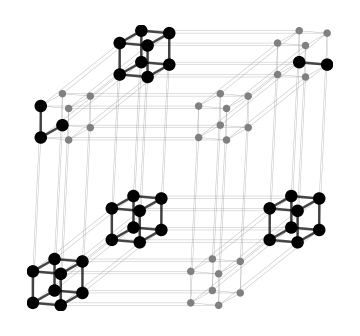

```mathematica
fig6cube=Show[graphplotcube2[cubemuts,Join[scube,scube1,scube5,scube15,scubemut, scube5mut, scube1mut,scube15mut]],graphplotcube[cubemuts,Join[scube,scube1,scube5,scube15,scubemut, scube5mut, scube1mut,scube15mut]],ImageSize->Medium]
```

```mathematica
labs=Table[StringRiffle[Table[If[site<0,ToString[site],"+"<>ToString[site]],{site,MutatedSites}]," "],{MutatedSites,Subsets[majorsites,{1}]}];
```

```mathematica
arrowends=.5cubecoords[[Range[1,64,8]]][[{5,3,2}]];
```

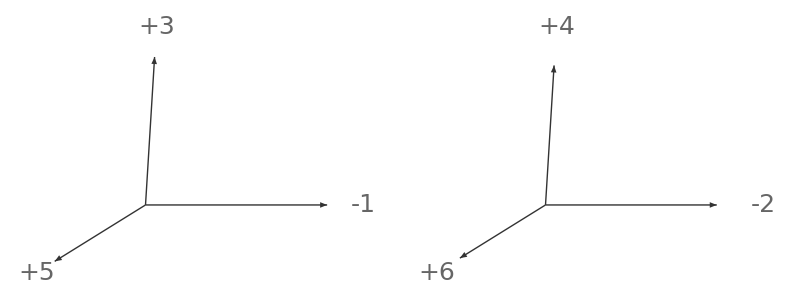

```mathematica
figaxes=Grid[{{Show[Graphics[{Arrowheads[.1],GrayLevel[.2],Arrow[{{0,0},.75#}]}&/@arrowends,ImageSize->250],Table[Graphics[{Text[Style[labs[[;;3]][[i]],25,GrayLevel[.4]],.9arrowends[[i]]]},Axes->None,Ticks->None],{i,Length[arrowends]}]],Show[Graphics[{Arrowheads[.1],GrayLevel[.2],Arrow[{{0,0},.55#}]}&/@arrowends,ImageSize->200],Table[Graphics[{Text[Style[labs[[4;;]][[i]],25,GrayLevel[.4]],.7arrowends[[i]]]},Axes->None,Ticks->None],{i,Length[arrowends]}]]}},Spacings->1.5]
```

```mathematica
fig6cube
```

-Graphics-

```mathematica
fig6cube=Grid[{{fig6cube,Magnify[figaxes,.6]}},Spacings->0, Alignment->Bottom]
Export[StringJoin[figpath,"/5ss_6cube.pdf"],Rasterize[%,RasterSize->2000]];
```

-Graphics- | -Graphics-